```mathematica
Solve[4 x(1-x) == y, x]
```

{{x→1/2 (1-√(1-y))},{x→1/2 (1+√(1-y))}}

```mathematica
D[1/2 (1+√(1-y)), y]
```

-1/(4 √(1-y))

```mathematica
ρ[x_]:= 1/(π √(x(1-x)))
```

```mathematica
1/(4 √(1-x))(ρ[1/2(1-√(1-x))] + ρ[1/2(1+√(1-x))]) //ExpandAll
```

1/(π √(1-x) √x)

```mathematica
Integrate[1/(√(x(1-x))), {x, 0, 1}]
```

π

```mathematica
Abs[D[4x(1-x), x]]//Simplify
```

Abs[4-8 x]

```mathematica
f[x_]:= 4x(1-x)
```

```mathematica
Solve[x==f[x], x]
```

{{x→0},{x→3/4}}

```mathematica
Solve[Composition[f, f][x] == x, x]
```

{{x→0},{x→3/4},{x→1/8 (5-√5)},{x→1/8 (5+√5)}}

```mathematica
Solve[Composition[f, f, f][x] == x, x]
```

{{x→0},{x→3/4},{x→Root0.188Root[-7+56 #1-112 #1^2+64 #1^3&,1]0.18825509907063326},{x→Root0.611Root[-7+56 #1-112 #1^2+64 #1^3&,2]0.6112604669781572},{x→Root0.950Root[-7+56 #1-112 #1^2+64 #1^3&,3]0.9504844339512094},{x→Root0.117Root[-3+36 #1-96 #1^2+64 #1^3&,1]0.116977778440511},{x→Root0.413Root[-3+36 #1-96 #1^2+64 #1^3&,2]0.4131759111665349},{x→Root0.970Root[-3+36 #1-96 #1^2+64 #1^3&,3]0.9698463103929541}}

```mathematica
Solve[Composition[f, f, f, f][x] == x, x]
```

{{x→0},{x→3/4},{x→1/8 (5-√5)},{x→1/8 (5+√5)},{x→Root0.0432Root[1-32 #1+224 #1^2-448 #1^3+256 #1^4&,1]0.04322727117869955},{x→Root0.165Root[1-32 #1+224 #1^2-448 #1^3+256 #1^4&,2]0.1654346968205709},{x→Root0.552Root[1-32 #1+224 #1^2-448 #1^3+256 #1^4&,3]0.5522642316338267},{x→Root0.989Root[1-32 #1+224 #1^2-448 #1^3+256 #1^4&,4]0.9890738003669025},{x→Root0.0338Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,1]0.033763885297822115},{x→Root0.130Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,2]0.13049554138967037},{x→Root0.277Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,3]0.277130822111731},{x→Root0.454Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,4]0.4538658202683458},{x→Root0.637Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,5]0.6368314950361406},{x→Root0.801Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,6]0.8013173181892688},{x→Root0.925Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,7]0.9251085678638385},{x→Root0.991Root[17-816 #1+11424 #1^2-71808 #1^3+239360 #1^4-452608 #1^5+487424 #1^6-278528 #1^7+65536 #1^8&,8]0.9914865498425413}}

```mathematica
Solve[Composition[f, f, f, f, f][x] == x, x]
```

{{x→0},{x→3/4},{x→Root0.0794Root[-11+220 #1-1232 #1^2+2816 #1^3-2816 #1^4+1024 #1^5&,1]0.07937323358440938},{x→Root0.292Root[-11+220 #1-1232 #1^2+2816 #1^3-2816 #1^4+1024 #1^5&,2]0.29229249349905706},{x→Root0.571Root[-11+220 #1-1232 #1^2+2816 #1^3-2816 #1^4+1024 #1^5&,3]0.5711574191366443},{x→Root0.827Root[-11+220 #1-1232 #1^2+2816 #1^3-2816 #1^4+1024 #1^5&,4]0.8274303669726228},{x→Root0.980Root[-11+220 #1-1232 #1^2+2816 #1^3-2816 #1^4+1024 #1^5&,5]0.9797464868072483},{x→Root9.04 × 10^-3Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,1]0.009035651368646643},{x→Root0.0358Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,2]0.035816033491963696},{x→Root0.138Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,3]0.1381329809474653},{x→Root0.210Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,4]0.2099715452143998},{x→Root0.382Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,5]0.3821205322452936},{x→Root0.476Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,6]0.47620904208810644},{x→Root0.664Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,7]0.6635339816587437},{x→Root0.893Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,8]0.8930265473713056},{x→Root0.944Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,9]0.9444177243209502},{x→Root0.998Root[1-160 #1+6240 #1^2-92352 #1^3+682240 #1^4-2848768 #1^5+7135232 #1^6-10911744 #1^7+9961472 #1^8-4980736 #1^9+1048576 #1^10&,10]0.9977359612862126},{x→Root0.0102Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,1]0.010235029373752752},{x→Root0.0405Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,2]0.040521094189884685},{x→Root0.0896Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,3]0.08961827939636184},{x→Root0.156Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,4]0.1555165404621567},{x→Root0.236Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,5]0.23551799483651878},{x→Root0.326Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,6]0.32634737357758986},{x→Root0.424Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,7]0.42428611124771165},{x→Root0.525Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,8]0.5253245844193564},{x→Root0.625Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,9]0.6253262661293603},{x→Root0.720Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,10]0.7201970757788172},{x→Root0.806Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,11]0.8060529912738315},{x→Root0.879Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,12]0.8793790613463954},{x→Root0.937Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,13]0.937173308072291},{x→Root0.977Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,14]0.9770696282000244},{x→Root0.997Root[-31+4960 #1-236096 #1^2+5261568 #1^3-66646528 #1^4+533172224 #1^5-2870927360 #1^6+10827497472 #1^7-29297934336 #1^8+57567870976 #1^9-82239815680 #1^10+84515225600 #1^11-60850962432 #1^12+29125246976 #1^13-8321499136 #1^14+1073741824 #1^15&,15]0.9974346616959475}}

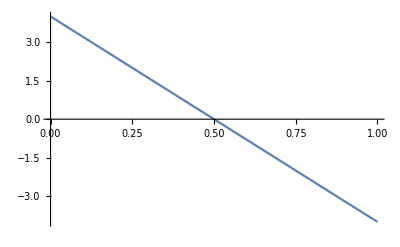

```mathematica
Plot[f'[x], {x, 0,1}]
```